# Cost of Flights and Distances

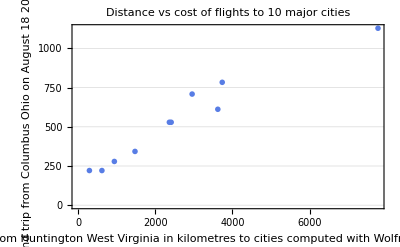

```mathematica
Block[{cities,travelAssociation},cities={Entity["City",{"Miami","Florida","UnitedStates"}],Entity["City",{"SanDiego","California","UnitedStates"}],Entity["City",{"NewYork","NewYork","UnitedStates"}],Entity["City",{"Chicago","Illinois","UnitedStates"}],Entity["City",{"Seattle","Washington","UnitedStates"}],Entity["City",{"SaltLakeCity","Utah","UnitedStates"}],Entity["City",{"Boston","Massachusetts","UnitedStates"}],Entity["City",{"Honolulu","Hawaii","UnitedStates"}],Entity["City",{"Denver","Colorado","UnitedStates"}],Entity["City",{"Boulder","Colorado","UnitedStates"}]};travelAssociation=AssociationThread[cities->Transpose[{(GeoDistance[Here,#1,UnitSystem->"Metric"]&)/@cities,{343,612,221,279,784,709,221,1129,529,529}}]];ListPlot[(Callout[travelAssociation[#1],#1["Name"]]&)/@cities,FrameLabel->{"Geodesic Distance from Huntington West Virginia in kilometres to cities computed with Wolfram Mathematica GeoDistance","Cost of cheapest round trip from Columbus Ohio on August 18 2022 from Google Flights"},LabelStyle->Directive[13,FontFamily->"JetBrains Mono"],Frame->True,ImageSize->Full,PlotTheme->"Business",PlotLabel->"Distance vs cost of flights to 10 major cities"]]
```

-Graphics-

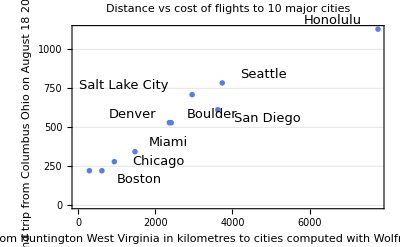

```mathematica
Block[{cities,travelAssociation},cities={Entity["City",{"Miami","Florida","UnitedStates"}],Entity["City",{"SanDiego","California","UnitedStates"}],Entity["City",{"NewYork","NewYork","UnitedStates"}],Entity["City",{"Chicago","Illinois","UnitedStates"}],Entity["City",{"Seattle","Washington","UnitedStates"}],Entity["City",{"SaltLakeCity","Utah","UnitedStates"}],Entity["City",{"Boston","Massachusetts","UnitedStates"}],Entity["City",{"Honolulu","Hawaii","UnitedStates"}],Entity["City",{"Denver","Colorado","UnitedStates"}],Entity["City",{"Boulder","Colorado","UnitedStates"}]};travelAssociation=AssociationThread[cities->Transpose[{(GeoDistance[Here,#1,UnitSystem->"Metric"]&)/@cities,{343,612,221,279,784,709,221,1129,529,529}}]];ListPlot[(Callout[travelAssociation[#1],#1["Name"],Appearance->"Leader"]&)/@cities,FrameLabel->{"Geodesic Distance from Huntington West Virginia in kilometres to cities computed with Wolfram Mathematica GeoDistance","Cost of cheapest round trip from Columbus Ohio on August 18 2022 from Google Flights"},LabelStyle->Directive[13,FontFamily->"JetBrains Mono"],Frame->True,ImageSize->Full,PlotTheme->"Business",PlotLabel->"Distance vs cost of flights to 10 major cities"]]
```

```mathematica
Block[{cities,travelAssociation},cities={Entity["City",{"Miami","Florida","UnitedStates"}],Entity["City",{"SanDiego","California","UnitedStates"}],Entity["City",{"NewYork","NewYork","UnitedStates"}],Entity["City",{"Chicago","Illinois","UnitedStates"}],Entity["City",{"Seattle","Washington","UnitedStates"}],Entity["City",{"SaltLakeCity","Utah","UnitedStates"}],Entity["City",{"Boston","Massachusetts","UnitedStates"}],Entity["City",{"Honolulu","Hawaii","UnitedStates"}],Entity["City",{"Denver","Colorado","UnitedStates"}],Entity["City",{"Boulder","Colorado","UnitedStates"}]};travelAssociation=AssociationThread[cities->Transpose[{(GeoDistance[Here,#1,UnitSystem->"Metric"]&)/@cities,{343,612,221,279,784,709,221,1129,529,529}}]];ListPlot[(Callout[travelAssociation[#1],#1["Name"]]&)/@cities,FrameLabel->{"Geodesic Distance from Huntington West Virginia in kilometres to cities computed with Wolfram Mathematica GeoDistance","Cost of cheapest round trip from Columbus Ohio on August 18 2022 from Google Flights"},LabelStyle->Directive[13,FontFamily->"JetBrains Mono"],Frame->True,ImageSize->Full,PlotTheme->"Business",PlotLabel->"Distance vs cost of flights to 10 major cities"]]
```

-Graphics-